```mathematica
img100=-Graphics-;
```

```mathematica
data=ImageData[img100];(*This is now a 2D array of pixel intensities*)
```

```mathematica
maxValue=Max[data];(*Find the maximum intensity*)
minValue=Min[data];

position=Position[data,maxValue];(*Get the position of the brightest pixel*)
```

```mathematica
croppedImage=ImageTake[img100,{position[[1]][[1]]-15,position[[1]][[1]]+15},{position[[1]][[2]]-15,position[[1]][[2]]+15}]
```

-Graphics-

```mathematica
bead100image=croppedImage;
```

```mathematica
imgdata=Flatten[Table[{i,j,ImageData[bead100image][[i,j]]},{i,Length[ImageData[bead100image]]},{j,Length[ImageData[bead100image][[i]]]}],1];
```

```mathematica
gaussianmodel=a Exp[-b ((x-x00)^2+(y-y00)^2)]+c;
```

```mathematica
fit=FindFit[imgdata,gaussianmodel,{{a,maxValue-minValue},b,{c,minValue},{x00,ImageDimensions[bead100image][[1]]/2},{y00,ImageDimensions[bead100image][[2]]/2}},{x,y}]
```

{a→933.774,b→0.371772,c→2466.59,x00→16.3006,y00→16.2286}

```mathematica
test2=-Graphics-;
```

```mathematica
imgdata2=Flatten[Table[{i,j,ImageData[test2][[i,j]]},{i,Length[ImageData[test2]]},{j,Length[ImageData[test2][[i]]]}],1];
```

```mathematica
fit2=FindFit[imgdata2,{gaussianmodel,{a+c>ImageMeasurements[test2,"Max"]}},{a,b,{c,0},{x0,ImageDimensions[test2][[1]]/2},{y0,ImageDimensions[test2][[2]]/2}},{x,y}]
```

FindFit::nrnum: The function value 1/2 ((-0.00314336+1. ⅇ^(-1. Plus[«2»]))^2+(-0.00314336+1. ⅇ^(-1. Plus[«2»]))^2+(-0.00314336+1. «1»)^2+(«1»)^2+(«1»)^2+«1»+«1»+(«1»)^2+(-«21»+1. «1»)^2+(-0.0030518+1. ⅇ^(-1. «1»))^2+«4086») is not a real number at {a,b,c,x0,y0} = {1.,1.,0.,32.,32.}.

IPOPTMinimize::badobj: Invalid objective function. The objective function doesn't evaluate to a real-valued numeric result at the initial point.

FindFit::nrgnum: The gradient is not a vector of real numbers at {a,b,c,x0,y0} = {1.,1.,0.,32.,32.}.

FindFit::grad: Evaluation of the gradient of function Experimental`NumericalFunction[«1»] failed at {1.,1.,0.,32.,32.}.

FindFit[1]
 |  |  |  |

```mathematica
Show[Plot3D[gaussianmodel/. fit2,{x,ImageDimensions[test2][[1]]/4,3*ImageDimensions[test2][[1]]/4},{y,ImageDimensions[test2][[2]]/4,3*ImageDimensions[test2][[2]]/4},PlotRange->All,PlotPoints->100,MaxRecursion->5],ListPointPlot3D[imgdata2,PlotStyle->Directive[PointSize[Medium],Red]],PlotRange->{{ImageDimensions[test2][[1]]/4,3*ImageDimensions[test2][[1]]/4},{ImageDimensions[test2][[2]]/4,3*ImageDimensions[test2][[2]]/4},All}]
```

General::ivar: 16.0003 is not a valid variable.

ReplaceAll::reps: {FindFit[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 16.0003 is not a valid variable.

ReplaceAll::reps: {FindFit[{{1.,1.,0.00314336},{1.,2.,0.00325017},{1.,3.,0.00300603},{1.,4.,0.00314336},«4»,{1.,9.,0.00318914},{1.,10.,0.00309758},«4086»},«3»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 16.3236 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

ReplaceAll::reps: {FindFit[«1»]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics3D-

```mathematica
0.25/0.046
```

5.43478

```mathematica
5.434782608695652^2
```

29.5369

```mathematica
dum2pixel[dum_]:=(dum/2)/(0.046*2)
```

```mathematica
dum2pixel[0.5]
```

2.71739

```mathematica
disc500=Piecewise[{{1,x^2+y^2<29.53686200378072}},0]
```

Piecewise[{{1, x^2+y^2<29.5369}, {0, True}}]

```mathematica
disc200=Piecewise[{{1,x^2+y^2<dum2pixel[0.2]^2}},0]
```

Piecewise[{{1, x^2+y^2<1.18147}, {0, True}}]

```mathematica
discgenerator[d_]:=Piecewise[{{1,x^2+y^2<dum2pixel[d]^2}},0]
```

```mathematica
discgeneratorfunc[d_,x0_,y0_]:=discgenerator[d]/. {x->x0,y->y0}
```

```mathematica
convolintensityfunc[d_]:=Table[NIntegrate[discgeneratorfunc[d,x,y]*(ⅇ^(-b ((x0-x)^2+(y0-y)^2))/.fit),{x,-Infinity,Infinity},{y,-Infinity,Infinity}],{x0,-50,50},{y0,-50,50}]
```

```mathematica
cov200=convolintensityfunc[0.2];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.0252782,0.483157}. NIntegrate obtained 1.03×10^-319 and 0. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.9337×10^-318 and 1.198×10^-320 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.831×10^-316 and 4.3705×10^-320 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.32759×10^-315 and 7.9055×10^-320 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.00238908,0.990258}. NIntegrate obtained 1.03×10^-319 and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.343749,0.00376287}. NIntegrate obtained 8.4806×10^-320 and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.0252782,0.483157}. NIntegrate obtained 1.03×10^-319 and 0. for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 6.9337×10^-318 and 1.198×10^-320 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.831×10^-316 and 4.3705×10^-320 for the integral and error estimates.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 2.32759×10^-315 and 7.9055×10^-320 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.00238908,0.990258}. NIntegrate obtained 1.03×10^-319 and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.343749,0.00376287}. NIntegrate obtained 8.4806×10^-320 and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

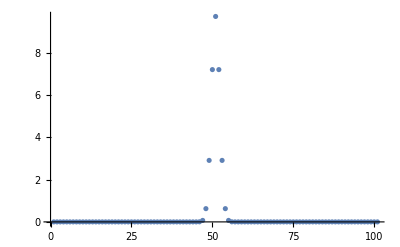

```mathematica
ListPlot[Total[convolintensityfunc[0.2]],PlotRange->All]
```

```mathematica
real=Total[ImageData[-Graphics-]]
```

{22329.,22401.1,22099.,22095.,22759.,22549.,22335.,22429.,22794.,22432.,22547.,22728.,22877.,22950.,22844.9,23504.9,23901.1,24698.,26471.,30867.,38217.,53043.,73689.,98228.,110693.,105898.,86580.,63795.,45644.9,34738.,28041.,25349.1,24400.9,23213.,22933.,22904.,22945.,22718.,22485.,22249.1,22743.,22665.,22339.,22584.,22153.,22448.,22494.,22064.,22448.6}

```mathematica
ListPlot[(%400-%400[[1]])/Max[%400]*70,PlotRange->All]
```

Part::partd: Part specification True⟦1⟧ is longer than depth of object.

ListPlot::lpn: (70. (True-1. True⟦1⟧))/True is not a list of numbers or pairs of numbers.

ListPlot[(70 (True-True⟦1⟧))/True,PlotRange→All]

```mathematica
ImageAdjust/@{-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

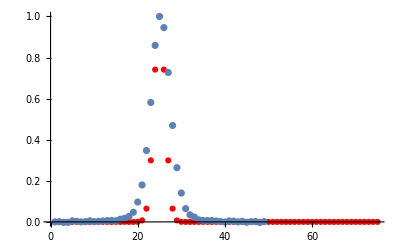

```mathematica
Show[ListPlot[Drop[Total[cov200]/Max[Total[cov200]],26],PlotRange->All,PlotStyle->Red],ListPlot[(real-real[[1]])/Max[real-real[[1]]],PlotRange->All]]
```

```mathematica
convolintensity
```

convolintensity

```mathematica
Total[convolintensity]
```

Total[convolintensity]

```mathematica
Interpolation[Total[convolintensity]]
```

Interpolation::innd: First argument in Total[convolintensity] does not contain a list of data and coordinates.

Interpolation[Total[convolintensity]]

```mathematica
Plot[%424[x],{x,1.,101.},PlotRange->All]
```

-Graphics-

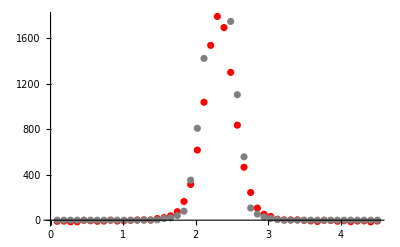
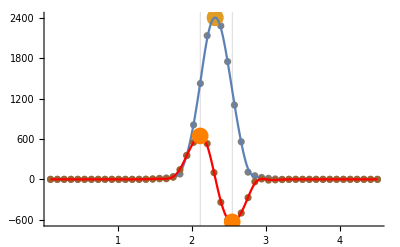
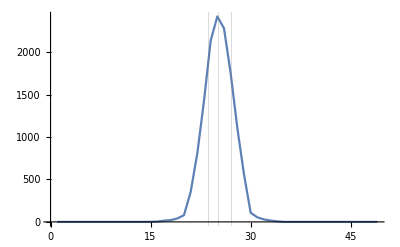
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
allplots[-Graphics-,5]
```

```mathematica
allinfo[-Graphics-,5]
```

{True,T,267.895,465.382,2403.51,0.505544,1.472,False,NA,NA,0.092 NA,0.776175,0.0362348,0.0320301,-0.0292727,-0.0376364,0.836273,0.916667,1.6071,-2.07662,0.0992338,0.900766,0.552899,L}

```mathematica
allinfo[-Graphics-,5]
```

{True,T,568.136,634.063,20133.5,0.764042,2.116,False,NA,NA,0.092 NA,1.05329,0.0448008,0.0475261,-0.0250909,0.,0.939817,0.984733,3.30308,-2.93741,0.0652228,0.934777,0.527539,L}

```mathematica
Total[convolintensity]
```

Total[convolintensity]

```mathematica
MatrixPlot[convolintensity]
```

MatrixPlot::mat0: Argument convolintensity at position 1 is not a matrix.

MatrixPlot[convolintensity]

```mathematica
ImageData[Image[convolintensity]]
```

Image::imgarray: The specified argument convolintensity should be an array of rank 2 or 3 with machine-sized numbers.

ImageData::imginv: Expecting an image or graphics instead of Image[convolintensity].

ImageData[Image[convolintensity]]

```mathematica
allinfo[ImageAdjust[Image[convolintensity]],5]
```

Image::imgarray: The specified argument convolintensity should be an array of rank 2 or 3 with machine-sized numbers.

ImageAdjust::imginv: Expecting an image or graphics instead of Image[convolintensity].

ImageData::imginv: Expecting an image or graphics instead of ImageAdjust[Image[convolintensity]].

ImageDimensions::imginv: Expecting an image or graphics instead of ImageAdjust[Image[convolintensity]].

Part::partw: Part 2 of ImageDimensions[ImageAdjust[Image[convolintensity]]] does not exist.

Part::pkspec1: The expression ImageDimensions[ImageAdjust[Image[convolintensity]]]⟦2⟧ cannot be used as a part specification.

ImageData::imginv: Expecting an image or graphics instead of ImageAdjust[Image[convolintensity]].

General::stop: Further output of ImageData::imginv will be suppressed during this calculation.

ImageDimensions::imginv: Expecting an image or graphics instead of ImageAdjust[Image[convolintensity]].

Part::pkspec1: The expression ImageAdjust[Image[convolintensity]] cannot be used as a part specification.

ImageDimensions::imginv: Expecting an image or graphics instead of ImageAdjust[Image[convolintensity]].

General::stop: Further output of ImageDimensions::imginv will be suppressed during this calculation.

Part::partw: Part 2 of ImageDimensions[ImageAdjust[Image[convolintensity]]] does not exist.

Part::pkspec1: The expression ImageAdjust[Image[convolintensity]] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Image`IntegrationDump`i:_Image?ImageQ|_Image3D?ImageQ.

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Hold[Image`IntegrationDump`resh].

If[Hold[RuleCondition[Image`IntegrationDump`res,With[{Image`IntegrationDump`r=Image`IntegrationDump`res},Hold[Image`IntegrationDump`r]=!=Image`IntegrationDump`resh]]]>0,If[intensitycheck[ImageAdjust[Image[convolintensity]],5]<intensitythreshold||backgroundbadcheck[ImageAdjust[Image[convolintensity]],5]||!backgrounddeletecomponentcheck[ImageAdjust[Image[convolintensity]],5]||Total[cleanYmean[ImageAdjust[Image[convolintensity]],5]]≤0,{boundarycheck[ImageAdjust[Image[convolintensity]],5],F or bad background,intensitycheck[ImageAdjust[Image[convolintensity]],5],Mean[backgroundintensities[ImageAdjust[Image[convolintensity]],5]],NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA},If[findintensitypeaks[ImageAdjust[Image[convolintensity]],5]=={},{boundarycheck[ImageAdjust[Image[convolintensity]],5],T,intensitycheck[ImageAdjust[Image[convolintensity]],5],meanbackground[ImageAdjust[Image[convolintensity]],5],NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA},Module[{intensitycheckresult$,signalstrength$,averagebackground$,meanYmainpeakintensityoverbackground$,widthX$,halfAreaWidth$,meanwidth$,secondpeakornot$,intensitysecondpeak$,secondpeakdirection$,peaksdistance$,tailornot$,directiontail$,lengthtail$,discR$,intensitycentroidtodisccenterx$,peaktodiscX$,brightesttodisccenterX$,brightesttodisccenterY$,diskcoverage$,polygoncoverage$,areaofKT$,tiltangle$,elongationratio$,semiaxesratio$,boundboxX$,leftrightratio$,skewdirec$},intensitycheckresult$=T;signalstrength$=intensitycheck[ImageAdjust[Image[convolintensity]],5];averagebackground$=meanbackground[ImageAdjust[Image[convolintensity]],5];meanYmainpeakintensityoverbackground$=mainpeak[ImageAdjust[Image[convolintensity]],5]⟦2⟧;meanwidth$=meanareawidth[ImageAdjust[Image[convolintensity]],5] pixelsize;boundboxX$=boundingboxX[ImageAdjust[Image[convolintensity]],5] pixelsize;secondpeakornot$=ifreallysecondpeak[ImageAdjust[Image[convolintensity]],5];intensitysecondpeak$=secondpeakintensity[ImageAdjust[Image[convolintensity]],5];secondpeakdirection$=directionsecondpeak[ImageAdjust[Image[convolintensity]],5];peaksdistance$=distancetwopeaks[ImageAdjust[Image[convolintensity]],5] pixelsize;discR$=boundingdiscRadius[ImageAdjust[Image[convolintensity]],5] pixelsize;brightesttodisccenterX$=brightesttodisccenter[ImageAdjust[Image[convolintensity]],5]⟦1⟧ pixelsize;brightesttodisccenterY$=brightesttodisccenter[ImageAdjust[Image[convolintensity]],5]⟦2⟧ pixelsize;diskcoverage$=boundingdiskcoverage[ImageAdjust[Image[convolintensity]],5];polygoncoverage$=convexcoverage[ImageAdjust[Image[convolintensity]],5];areaofKT$=areacomponentofinterest[ImageAdjust[Image[convolintensity]],5] pixelsize pixelsize;tiltangle$=angle[ImageAdjust[Image[convolintensity]],5];elongationratio$=elongation[ImageAdjust[Image[convolintensity]],5];semiaxesratio$=semiaxesRatio[ImageAdjust[Image[convolintensity]],5];leftrightratio$=leftrightarearatio[ImageAdjust[Image[convolintensity]],5];skewdirec$=skewdirection[ImageAdjust[Image[convolintensity]],5];intensitycentroidtodisccenterx$=N[intensitycentroidTodisccenterX[ImageAdjust[Image[convolintensity]],5] pixelsize];peaktodiscX$=peakTodisccenterX[ImageAdjust[Image[convolintensity]],5] pixelsize;{boundarycheck[ImageAdjust[Image[convolintensity]],5],intensitycheckresult$,signalstrength$,averagebackground$,meanYmainpeakintensityoverbackground$,meanwidth$,boundboxX$,secondpeakornot$,intensitysecondpeak$,secondpeakdirection$,peaksdistance$,discR$,intensitycentroidtodisccenterx$,peaktodiscX$,brightesttodisccenterX$,brightesttodisccenterY$,diskcoverage$,polygoncoverage$,areaofKT$,tiltangle$,elongationratio$,semiaxesratio$,leftrightratio$,skewdirec$}]]],{boundarycheck[ImageAdjust[Image[convolintensity]],5],NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA}]

```mathematica
convtable=Table[convolintensityfunc[d/10],{d,1,10}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 7.25303×10^-318 and 1.5074×10^-320 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.81112×10^-315 and 1.0129×10^-319 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.81112×10^-315 and 1.01417×10^-319 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.193359,0.0218858}. NIntegrate obtained 2.30185×10^-319 and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.108154,0.870129}. NIntegrate obtained 2.30185×10^-319 and 0. for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 18 recursive bisections in x near {x,y} = {0.277343,0.00618954}. NIntegrate obtained 2.29573×10^-319 and 0. for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
Table[{{"d=",d/10},allinfo[ImageAdjust[Image[convtable[[d]]]],5]},{d,2,10}]
```

{{{d=,1/5},{False,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA}},{{d=,3/10},{False,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA}},{{d=,2/5},{False,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA}},{{d=,1/2},{False,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA}},{{d=,3/5},{False,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA}},{{d=,7/10},{False,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA}},{{d=,4/5},{False,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA}},{{d=,9/10},{False,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA}},{{d=,1},{False,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA,NA}}}

```mathematica
simutable={{{"d=",1/5},{0.000028573631401648782,0.0549205707517275,0.2540271107871245,0.14858360255374517,0.3029773025633908,0.874,False,"NA","NA",0.046 "NA",False,"right",0.1500135553935624,0.4165477163543212,0.,0.,1.0131570767557239,0.970260223048327,0.558624,0.,0.,1.}},{{"d=",3/10},{0.00006882310366019869,0.06519268381294194,0.2875980182601899,0.17107564934877104,0.3378896405362953,0.874,False,"NA","NA",0.046 "NA",False,"right",0.16679900913009493,0.43396313207460374,0.,0.,1.0193069389031502,0.9726962457337884,0.60835,0.,0.,1.}},{{"d=",2/5},{0.000053776431647696707,0.08009716660599189,0.34055591031512644,0.1996917068523281,0.3855655164498836,0.966,False,"NA","NA",0.046 "NA",False,"right",0.1932779551575632,0.4889867073857939,0.,0.,1.0056338882089668,0.9780821917808219,0.760702,0.,1.1102230246251565*^-16,0.9999999999999999}},{{"d=",1/2},{0.00013056007473065263,0.09902187433525404,0.41285668411283405,0.23253938843386776,0.4438406242783931,1.058,False,"NA","NA",0.046 "NA",False,"right",0.22942834205641705,0.508086606790614,0.,0.,1.0045025096783557,0.9697732997481108,0.822066,0.,0.,1.}},{{"d=",3/5},{0.00015750142580636225,0.1204783252340661,0.49618370891846236,0.2681497401819535,0.5097953273770152,1.15,False,"NA","NA",0.046 "NA",False,"right",0.271091854459231,0.5558201147853503,0.,0.,1.0137951854483744,0.9587628865979382,0.991346,0.,0.,1.}},{{"d=",7/10},{0.00015986478220635637,0.1429115972877023,0.5849050697230691,0.30553363895036234,0.5805875704779286,1.242,False,"NA","NA",0.046 "NA",False,"right",0.3154525348615346,0.6050355361464317,0.,0.,1.0174876708649494,0.9787610619469026,1.178612,0.,0.,1.}},{{"d=",4/5},{0.00019780488424976395,0.16543388538037168,0.6766981641549503,0.34408954198942565,0.6541346561831713,1.334,False,"NA","NA",0.046 "NA",False,"right",0.3613490820774748,0.6505382386916237,0.,0.,1.0074507897716973,0.9693721286370598,1.3478919999999999,0.,1.1102230246251565*^-16,0.9999999999999999}},{{"d=",9/10},{0.0002711744450380023,0.18778167966678685,0.7704286942782803,0.3834528421421343,0.7292070107345237,1.426,False,"NA","NA",0.046 "NA",False,"right",0.4082143471391403,0.6915316334051538,0.,0.,1.0098592406804332,0.9728629579375847,1.526694,0.,0.,1.}},{{"d=",1},{0.00019146609629889857,0.20995267733005646,0.8654631299929894,0.4233988072214889,0.8051721747485213,1.518,False,"NA","NA",0.046 "NA",False,"right",0.4557315649964947,0.7544560954754094,0.,0.,1.0093618323969271,0.9815880322209436,1.81447,0.,0.,1.}}};
```

```mathematica
Transpose[Transpose[simutable][[1]]][[2]]
```

{1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}

```mathematica
Transpose[Transpose[simutable][[2]]][[3]]
```

{0.254027,0.287598,0.340556,0.412857,0.496184,0.584905,0.676698,0.770429,0.865463}

```mathematica
Transpose[Transpose[simutable][[2]]][[4]]
```

{0.148584,0.171076,0.199692,0.232539,0.26815,0.305534,0.34409,0.383453,0.423399}

```mathematica
Transpose[Transpose[simutable][[2]]][[5]]
```

{0.302977,0.33789,0.385566,0.443841,0.509795,0.580588,0.654135,0.729207,0.805172}

```mathematica
Transpose[Transpose[simutable][[2]]][[6]]
```

{0.874,0.874,0.966,1.058,1.15,1.242,1.334,1.426,1.518}

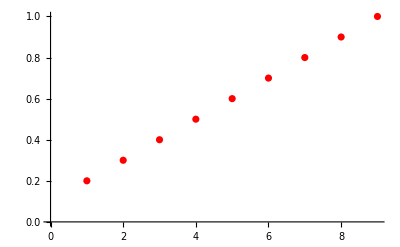

```mathematica
ListPlot[Transpose[Transpose[simutable][[1]]][[2]],PlotStyle->{Red,Thick}]
```

```mathematica
widthtable=Table[{{"d=",d/10},widthinfo[ImageAdjust[Image[convtable[[d]]]],5]},{d,1,10}]
```

{{{d=,1/10},{0.273831,0.120932,0.293282,1.38,0.256483}},{{d=,1/5},{0.287036,0.13266,0.310878,1.38,0.275493}},{{d=,3/10},{0.314576,0.154822,0.345547,1.38,0.312212}},{{d=,2/5},{0.359227,0.178719,0.38744,1.38,0.354654}},{{d=,1/2},{0.419592,0.213773,0.447758,1.564,0.410514}},{{d=,3/5},{0.501474,0.245586,0.508013,1.564,0.465922}},{{d=,7/10},{0.580033,0.280933,0.572372,1.748,0.524048}},{{d=,4/5},{0.67206,0.322423,0.650729,1.748,0.592829}},{{d=,9/10},{0.757474,0.361897,0.728478,1.932,0.65993}},{{d=,1},{0.860394,0.40037,0.811573,2.116,0.727733}}}

```mathematica
Transpose[Transpose[widthtable][[1]]][[2]]
```

{1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}

```mathematica
Transpose[Transpose[widthtable][[2]]][[1]]
```

{0.273831,0.287036,0.314576,0.359227,0.419592,0.501474,0.580033,0.67206,0.757474,0.860394}

```mathematica
Transpose[Transpose[widthtable][[2]]][[2]]
```

{0.120932,0.13266,0.154822,0.178719,0.213773,0.245586,0.280933,0.322423,0.361897,0.40037}

```mathematica
Transpose[Transpose[widthtable][[2]]][[3]]
```

{0.293282,0.310878,0.345547,0.38744,0.447758,0.508013,0.572372,0.650729,0.728478,0.811573}

```mathematica
Transpose[Transpose[widthtable][[2]]][[4]]
```

{1.38,1.38,1.38,1.38,1.564,1.564,1.748,1.748,1.932,2.116}

```mathematica
Transpose[Transpose[widthtable][[2]]][[5]]
```

{0.256483,0.275493,0.312212,0.354654,0.410514,0.465922,0.524048,0.592829,0.65993,0.727733}

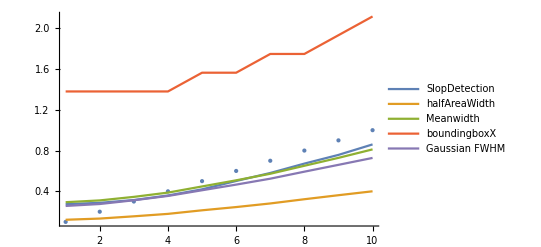

-Graphics-

```mathematica
Show[ListPlot[Transpose[Transpose[widthtable][[1]]][[2]],PlotStyle->{PointSize[Large]}],ListLinePlot[{Transpose[Transpose[widthtable][[2]]][[1]],Transpose[Transpose[widthtable][[2]]][[2]],Transpose[Transpose[widthtable][[2]]][[3]],Transpose[Transpose[widthtable][[2]]][[4]],Transpose[Transpose[widthtable][[2]]][[5]]},PlotLegends->{"SlopDetection","halfAreaWidth","Meanwidth","boundingboxX","Gaussian FWHM"}],PlotRange->All]
```

```mathematica
(*

*)
```